```mathematica
Needs["PlotLegends`"]
eps=4/100;
p=5/10;
c=1;
τ=12/100;

(* geometry: *)
T[x_]=10 τ c(0.2969 √(x/c)-0.126(x/c)-0.3537(x/c)^2+0.2843(x/c)^3-0.1015(x/c)^4);
Y[x_]=Piecewise[{{(eps x)/p^2(2 p - x/c), 0 ≤ x/c ≤ p },{(eps(c-x))/(1-p)^2(1+x/c-2p) ,p < x/c ≤ 1 }}];

(* solve for vorticity: *)
s[θ_]=Simplify[D[Y[x],x]/.x->c/2(1-Cos[θ])];
A0[α_]=Simplify[α-1/π Integrate[s[θ],{θ,0,π}]];
A1=Simplify[2/π Integrate[Cos[θ]s[θ],{θ,0,π}]];
Am[m_]=Assuming[m∈Integers,Simplify[2/π Integrate[Cos[m θ]s[θ],{θ,0,π}]]];
g[θ_,α_]=Simplify[2 Vinf(A0[α](1+Cos[θ])/Sin[θ]+A1 Sin[θ]+Sum[Am[n],{n,2,∞}])];
gx[x_,α_]=g[ArcCos[1-2 x/c],α];

(* velocity from thickness: *)
ut[x_]=Assuming[0<x<1,Simplify[Vinf/(2π)Integrate[D[T[xp],xp]/(x-xp),{xp,0,1},PrincipalValue->True]]];
vtPlus[x_]=1/2 Vinf D[T[x],x];
vtMinus[x_]=-vtPlus[x];

(* velocity from thickness with Riegels correction *)
vTanRiegels[x_]=(Vinf+ut[x])/(√(1+D[T[x]/2,x]^2));
utR[x_]=vTanRiegels[x] 1/(√(1+D[T[x]/2,x]^2))-Vinf;
vtPlusR[x_]=vTanRiegels[x] D[T[x]/2,x]/(√(1+D[T[x]/2,x]^2));
vtMinusR[x_]=-vtPlusR[x];

(* velocity from camber: *)
ucPlus[x_,α_]=1/2 gx[x,α];
ucMinus[x_,α_]=-ucPlus[x,α];
vc[x_,α_]=Assuming[{α∈Reals,0<x<1},-1/(2π)Integrate[gx[xp,α] 1/(x-xp),{xp,0,1},PrincipalValue->True]];

(* Cp *)
CpU[x_,α_]=1-((Vinf α+vtPlus[x]+vc[x,α])^2+(Vinf+ut[x]+ucPlus[x,α])^2)/Vinf^2;
CpL[x_,α_]=1-((Vinf α +vtMinus[x]+vc[x,α])^2+(Vinf+ut[x]+ucMinus[x,α])^2)/Vinf^2;
CpURiegels[x_,α_]=1-((Vinf α+vtPlusR[x]+vc[x,α])^2+(Vinf+utR[x]+ucPlus[x,α])^2)/Vinf^2;
CpLRiegels[x_,α_]=1-((Vinf α +vtMinusR[x]+vc[x,α])^2+(Vinf+utR[x]+ucMinus[x,α])^2)/Vinf^2;
```

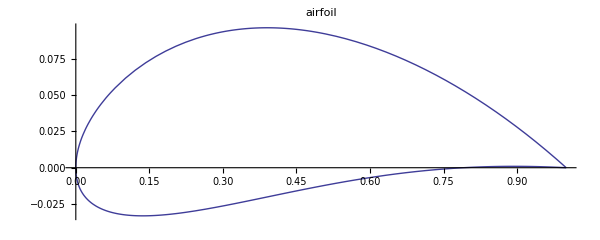

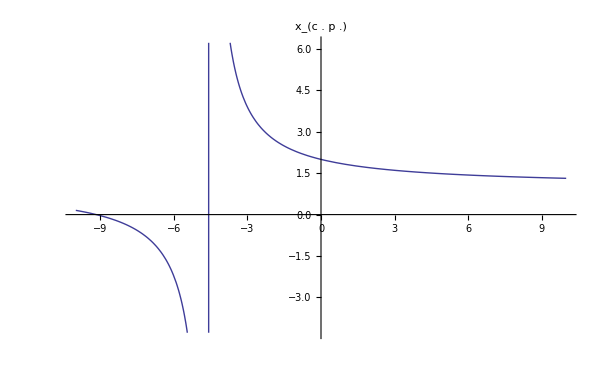

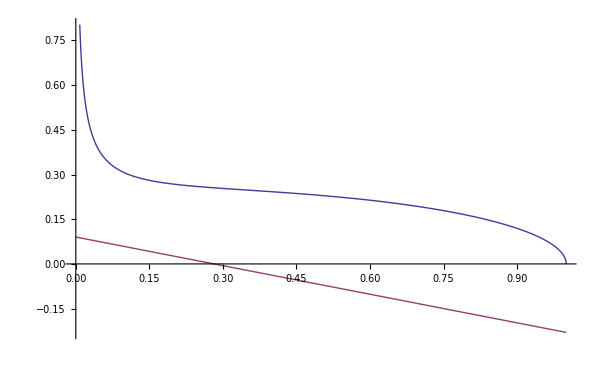

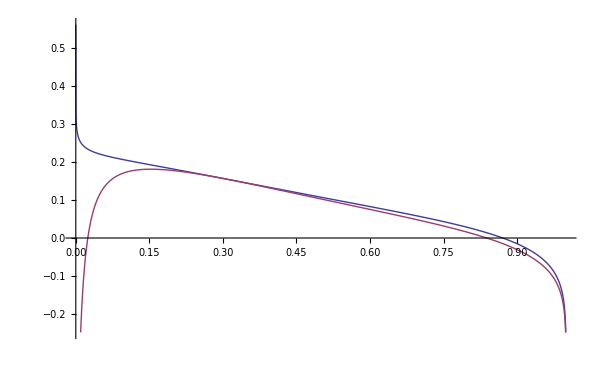

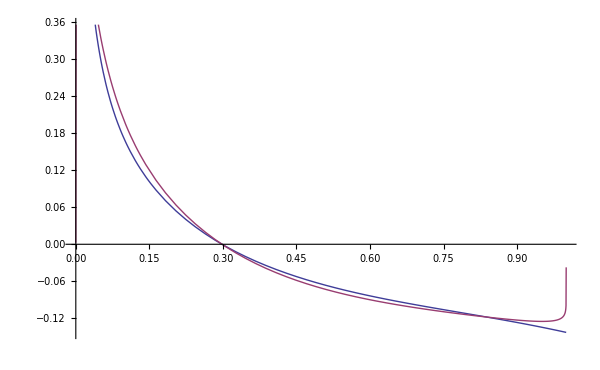

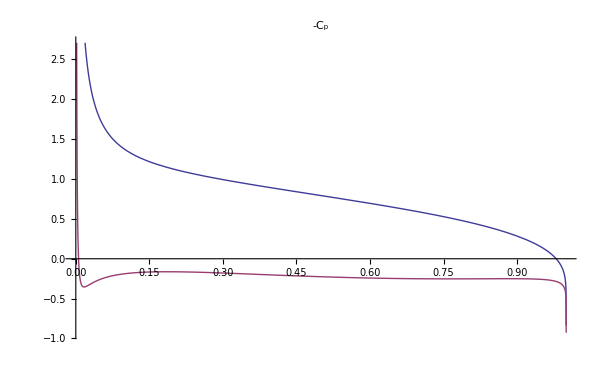

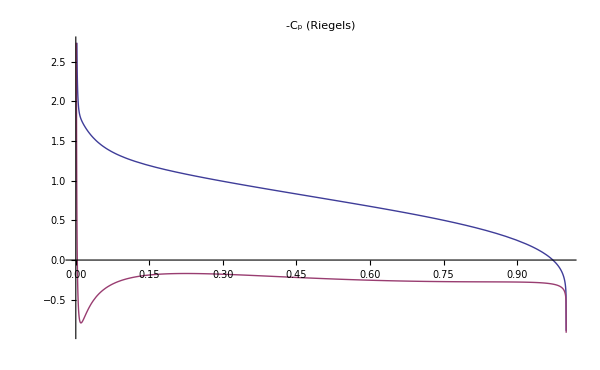

```mathematica
(* Plot airfoil *)
Plot[Y[x]+{T[x]/2,-T[x]/2},{x,0,1},AspectRatio->Automatic,ImageSize->600,PlotLabel->Style["airfoil",FontSize->20]]
(* plot x_(c.p.) *)
Plot[(4/25+α π/180)/(2/25+α π/180),{α,-10,10},ImageSize->600,PlotLabel->Style["x_(c . p .)",FontSize->20]]
Plot[{ucPlus[x,4*π/180]/Vinf,vc[x,4*π/180]/Vinf},{x,0,1},PlotLegend->{"u_c/(V_∞)","v_c/(V_∞)"},LegendPosition->{1.1,-0.3},ImageSize->600]
Plot[{ut[x]/Vinf,utR[x]/Vinf},{x,0,1},PlotLegend->{"u_t/(V_∞)","u_t/(V_∞) (Riegels)"},LegendPosition->{1.1,-0.3},ImageSize->600]
Plot[{vtPlus[x]/Vinf,vtPlusR[x]/Vinf},{x,0,1},PlotLegend->{"v_t/(V_∞)","v_t/(V_∞) (Riegels)"},LegendPosition->{1.1,-0.3},ImageSize->600]
Plot[{-CpU[x,4 π/180],-CpL[x,4 π/180]},{x,0,1},PlotLabel->Style["-C_p",FontSize->20]]
Plot[{-CpURiegels[x,4 π/180],-CpLRiegels[x,4 π/180]},{x,0,1},PlotLabel->Style["-C_p (Riegels)",FontSize->20]]
```

```mathematica
Manipulate[Plot[{-CpU[x,α π/180],-CpL[x,α π/180]},{x,0,1}],{{α,4},-10,10}]
Manipulate[Plot[{-CpU[x,α π/180],-CpL[x,α π/180],-CpURiegels[x,α π/180],-CpLRiegels[x,α π/180]},{x,0,1}],{{α,4},-10,10}]
Manipulate[{Plot[{-CpU[x,α π/180],-CpL[x,α π/180]},{x,0.0001,1},ImageSize->500],Plot[{-CpURiegels[x,α π/180],-CpLRiegels[x,α π/180]},{x,0.0001,1},ImageSize->500]},{{α,4},-10,10}]
```

```mathematica
Cl=Assuming[0<p<1,Simplify[2π(A0+A1/2)]];
Cmac=Assuming[0<p<1,Simplify[-π/4(A1-Am[2])]];
xcp=Assuming[0<p<1,Simplify[c/4((A0+A1-1/2 Am[2])/(A0+1/2 A1))]];
```

```mathematica
Integrate[(p-1/2(1-Cos[θp])),θp]
Integrate[Cos[m θp](p-1/2(1-Cos[θp])),θp]
```

Sin[θp]/2

(-Cos[m θp] Sin[θp]+m Cos[θp] Sin[m θp])/(2 (-1+m^2))